```mathematica
h=1/Tan[0.5*Pi/180*75]
w=h/1.777;
f=10;
n=1;
PerspectiveMatrix ={
{w, 0, 0, 0},
{0, h, 0, 0},
{0, 0, f/(f-n), 1},
{0, 0, -(n*f)/(f-n),0}
}
mat=Inverse[PerspectiveMatrix]

TransformPoint[p_,mat_]:=(
val=({p[[1]],p[[2]],p[[3]],1}.mat);
val[[1]]=val[[1]]/val[[4]];
val[[2]]=val[[2]]/val[[4]];
val[[3]]=val[[3]]/val[[4]];
Return[val[[1;;3]]])
LineHelper[p1_,p2_,mat_]:=Line[{TransformPoint[p1,mat],TransformPoint[p2,mat]}];
Graphics3D[{
LineHelper[{0,0,0},{0,0,1},mat],
LineHelper[{0,0,1},{0,1,1},mat],
LineHelper[{0,1,1},{0,1,0},mat],
LineHelper[{0,1,0},{0,0,0},mat],
LineHelper[{1,0,0},{1,0,1},mat],
LineHelper[{1,0,1},{1,1,1},mat],
LineHelper[{1,1,1},{1,1,0},mat],
LineHelper[{1,1,0},{1,0,0},mat],
LineHelper[{0,0,0},{1,0,0},mat],
LineHelper[{0,0,1},{1,0,1},mat],
LineHelper[{0,1,1},{1,1,1},mat],
LineHelper[{0,1,0},{1,1,0},mat]
},Axes->True,AxesLabel->{x,y,z}, Boxed->False]
```

1.30323

{{0.733385,0,0,0},{0,1.30323,0,0},{0,0,10/9,1},{0,0,-10/9,0}}

{{1.36354,0.,0.,0.},{0.,0.767327,0.,0.},{0.,0.,0.,-0.9},{0.,0.,1.,1.}}

-Graphics3D-

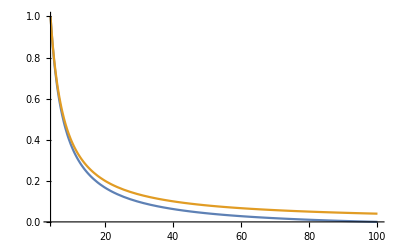

```mathematica
n=4; f=100;
Plot[{(n (f-z))/((f-n) z),n/z}, {z,4, 100},PlotRange->Full]
```

```mathematica
}
```

```mathematica
Clear[f,n,fl,sensx,sensy,fovy]
t=Tan[fovy];
now={
{1/(t*sensx/sensy),0,0,0},
{0,-1/t,0,0},
{0,0,0,n},
{0,0,-1,0}
}.{x,y,z,1};
now=now/now[[4]]
FullSimplify[now[[3]]]
```

{-(sensy x Cot[fovy])/(sensx z),(y Cot[fovy])/z,-n/z,1}

-n/z

```mathematica
Clear[f,n,fl,sensx,sensy,fovy]
FullSimplify[((-f/(n-f)-1)z-(n*f)/(n-f))/-z]
```

-(n (f+z))/((f-n) z)

```mathematica
Limit[(n (f-z))/((f-n) z),f->Infinity]
```

n/z

```mathematica
n/z=zl
zl*z=n
n/zl
```